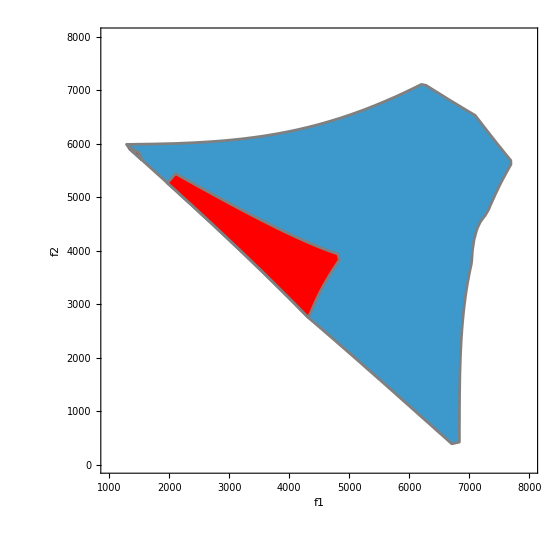

```mathematica
x1=f1;
x2=f2;
x3=10000-f1-f2;
x5=10000-f1-f2;
x8=10000-f1-f2;
e=35;
rho=15;
sigma=0.02;
link1=18*(1+0.15*(x1/3600)^4);
link2=22.5*(1+0.15*(x2/3600)^4);
link3=12*(1+0.15*(x3/1800)^4);
link5=2.4*(1+0.15*(x5/1800)^4);
link8=12*(1+0.15*(x8/1800)^4);
path1=link1+rho*(1-Exp[-sigma*link1]);
path2=link2+rho*(1-Exp[-sigma*link2]);
path5=link3+link5+link8+rho*(1-Exp[-sigma*(link3+link5+link8)]);
m1=20;
m2=15;
m5=2;
p1=RegionPlot[Abs[path1-path2]<=e&&Abs[path1-path5]<=e&&Abs[path2-path5]<=e&&(path1-path2)*(m1-m2)<0&&(path1-path5)*(m1-m5)<0&&(path2-path5)*(m2-m5)<0&&10000-f1-f2>=0,{f1,1000,8000},{f2,0,8000},Axes->True,Mesh->None,BoundaryStyle->Gray,PlotStyle->Red,FrameTicksStyle->Directive[Gray,FontSize->12],FrameLabel->{Style["f1",15],Style["f2",15]}];
p2=RegionPlot[Abs[path1-path2]<=e&&Abs[path1-path5]<=e&&Abs[path2-path5]<=e,{f1,1000,8000},{f2,0,8000},Axes->True,Mesh->None,BoundaryStyle->Gray,PlotStyle->bule,FrameTicksStyle->Directive[Gray,FontSize->12],FrameLabel->{Style["f1",15],Style["f2",15]}];
p=Show[p2,p1]
(*Export["ee35.eps",p];*)
```